# Chirped Detuned Raman Transfer

## Gabriel Patenotte || September 7, 2021 || Ni Group

## Notebook setup

```mathematica
Remove["Global`*"](*Clears all variables*)
padding={{70, 10}, {50, 10}}; (*Extra space surrounding a plot. Needs to be defined, else plots of the same ImageSize won't line up.*)
size=500; (*Size used for the ImageSize parameter*)
SetOptions[Plot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,ImagePadding->padding,ImageSize->size]; (*Sets Plots to have a certain look*)
SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True,FrameTicks->{Automatic,Automatic},ImagePadding->padding,ImageSize->size]; (*Sets ListPlots to have a certain look*)
```

```mathematica
messageHandler=If[Last[#],Abort[]]&

Internal`AddHandler["Message",messageHandler]
```

If[Last[#1],Abort[]]&

## Physics setup

```mathematica
μs=10^-6; (*Units*)
MHz=10^6; (*Units*)
GHz=10^9; (*Units*)
Γ=2π 100 MHz; (*Scattering from intermediate states*);
Δp=2π  7.5GHz; (*Detuning of the pump beam*)
ranget={0,40,.05};
ΔACassumed=2.59375MHz;
(*Range (in μs) and steps size (in μs) over which the ndsolve calculates the population in each state*)
```

```mathematica
H[t_,Ωs_,Ωp_,Δ0_,Δ1_]=({{0, 1/2 Ωp, 1/2 11Ωp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2 11Ωp, 0, Δp+2π 3.4 GHz-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, Δ0+Δ1 t-ⅈ 1032}}); (*Hamiltonian for a 4-level Λ system, with two excited intermediate states.*)
```

## Modules

```mathematica
findACShift[Ωs0_,Ωp0_]:=Module[{Ωs=Ωs0,Ωp=Ωp0},
P[t_]={p1[t],p2[t],p3[t],p4[t]};(*The population of the four states*)
init=P[0]=={1,0,0,0};(*The population is initially in the initial state*)
SE=ⅈ P'[t]==H[t,Ωs,Ωp,Δ0,0].P[t];(*The Schodinger equation*)
sols=ParametricNDSolve[{SE,init},{p1,p2,p3,p4},{t,1 μs},{Δ0},PrecisionGoal->7];
(*A parametric NDsolver, that gives a time-dependent solution as a function of Δ0*)
acData=Table[{Δ0,Abs[(p1[Δ0 MHz]/.sols)[1μs]]^2},{Δ0,-9,-6,.1}];
parabola=Fit[acData,{1,x,x^2},x];
{Solve[D[parabola,x]==0,x]⟦1,1,2⟧,Show[Plot[parabola,{x,-10,-5}],ListPlot[acData,Joined->False,PlotStyle->Blue]]}
]
```

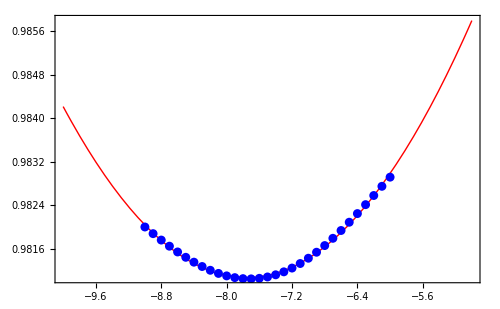
{-7.75375,-Graphics-}

```mathematica
findACShift[2π 120 MHz,2π .4 25 MHz]
```

```mathematica
scanΩs=Table[{Ωs,findACShift[2π Ωs MHz,2π 37 MHz]},{Ωs,1,250,20}];
scanΩp=Table[{Ωp,findACShift[2π 222 MHz,2π Ωp MHz]},{Ωp,1,50,5}];
```

```mathematica
scanΩsInterp=Interpolation[scanΩs];
scanΩpInterp=Interpolation[scanΩp];
```

```mathematica
FindRoot[scanΩsInterp[x]-1,{x,160}]⟦1,2⟧
FindRoot[scanΩpInterp[x]-3,{x,30}]⟦1,2⟧
```

165.775

30.7099

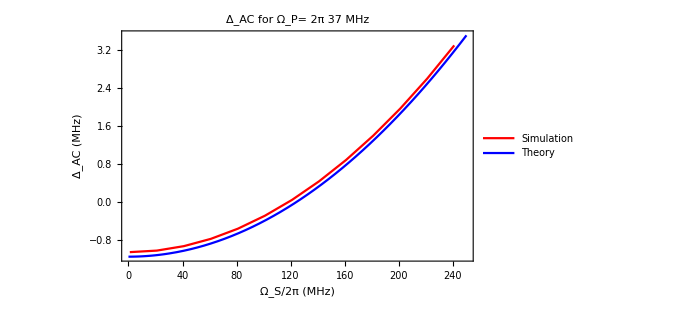

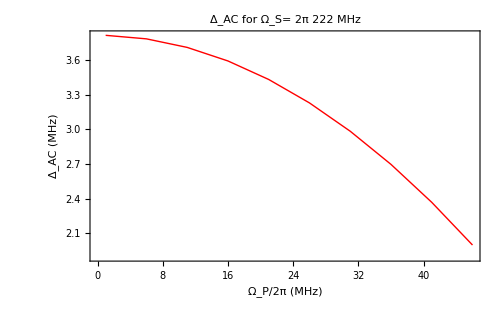

```mathematica
Show[ListPlot[scanΩs,PlotLabel->"Δ_AC for Ω_P= 2π 37 MHz",FrameLabel->{"Ω_S/2π (MHz)","Δ_AC (MHz)"},PlotLegends-> {"Simulation"}],Plot[1/MHz((2π MHz Ωs)^2-(2π 37 MHz)^2)/(4 2π 21 GHz)-1/MHz(12(2π 37 MHz)^2)/(4 2π (21+3.4) GHz),{Ωs,0,250},PlotStyle->Blue,PlotLegends-> {"Theory"}],PlotRange-> All]
ListPlot[scanΩp,PlotLabel->"Δ_AC for Ω_S= 2π 222 MHz",FrameLabel->{"Ω_P/2π (MHz)","Δ_AC (MHz)"}]
```

```mathematica
37*.4
```

14.8

```mathematica
findPops[Ωs0_,Ωp0_,Δ00_,Δ10_]:=Module[{Ωs=Ωs0,Ωp=Ωp0,Δ0=Δ00,Δ1=Δ10},
P[t_]={p1[t],p2[t],p3[t],p4[t]};
(*The population in each of the four bare basis state*)
init=P[0]=={1,0,0,0};(*The population initially resides in the initial state*) 
SE=ⅈ P'[t]==H[t,Ωs,Ωp,Δ0,Δ1].P[t];(*The Schrodinger equation*)
sols=NDSolveValue[{SE,init},{p1,p2,p3,p4},{t,0,20μs},PrecisionGoal->8];(*We solve the Schrodinger equation. The Method is chosen to significantly reduce the evaluation time.*)
pops=Abs[#[t μs]&/@sols]^2 (*The population in each state as a function of time. The use of # here gives each of the four outputs of sols an argument of t in μs.*);{lp1,lp2,lp3,lp4}=Table[Table[{t,pops⟦i⟧},{t,0,20,.05}],{i,1,4}](*Data for a ListPlot of the four populations over time.*)]
```

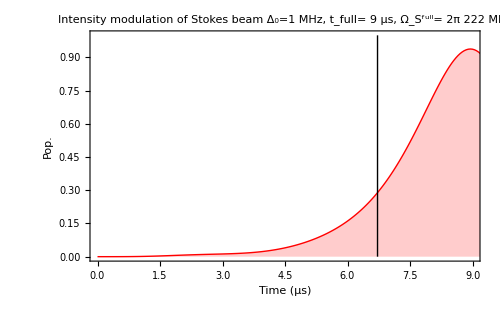

```mathematica
center=1MHz;
full=9μs;
ΩsMax=2π 222 MHz;
timeRes=(2π MHz)/ΩsMax FindRoot[scanΩsInterp[x]-center/MHz,{x,160}]⟦1,2⟧full/μs;
test1=findPops[ΩsMax t/full, 2π 37 MHz,center,0];
ListPlot[test1⟦4⟧,PlotRange->{{0,full/μs},{0,1}},Filling-> Axis,FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["Intensity modulation of Stokes beam \n Δ_0=`` MHz, t_full= `` μs, Ω_S^full= 2π `` MHz",center/MHz,full/μs,ΩsMax/(2π MHz)],Epilog->Line[{{timeRes,0},{timeRes,1}}]]
```

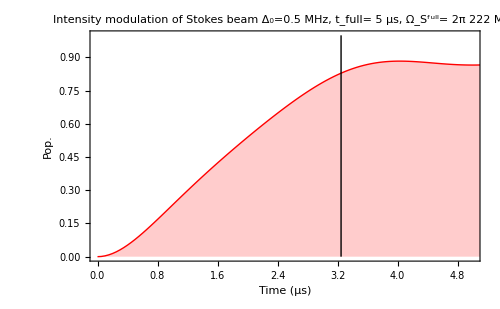

```mathematica
center=.5MHz;
full=5μs;
ΩsMax=2π 222 MHz;
timeRes=(2π MHz)/ΩsMax FindRoot[scanΩsInterp[x]-center/MHz,{x,160}]⟦1,2⟧full/μs;
test1=findPops[ΩsMax (1-t/full), 2π 37 MHz,center,0];
ListPlot[test1⟦4⟧,PlotRange->{{0,full/μs},{0,1}},Filling-> Axis,FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["Intensity modulation of Stokes beam \n Δ_0=`` MHz, t_full= `` μs, Ω_S^full= 2π `` MHz",center/MHz,full/μs,ΩsMax/(2π MHz)],Epilog->Line[{{timeRes,0},{timeRes,1}}]]
```

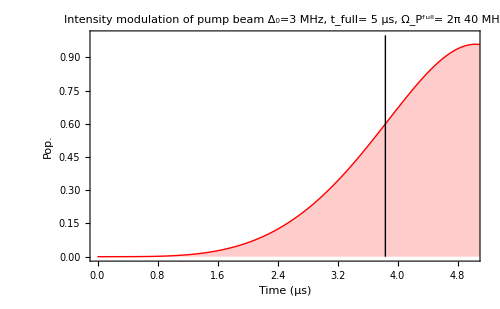

```mathematica
center=3MHz;
full=5μs;
ΩpMax=2π 40 MHz;
timeRes=(2π MHz)/ΩpMax FindRoot[scanΩpInterp[x]-center/MHz,{x,30}]⟦1,2⟧full/μs;
test1=findPops[2π 222 MHz,ΩpMax t/full ,center,0];
ListPlot[test1⟦4⟧,PlotRange->{{0,full/μs},{0,1}},Filling-> Axis,FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["Intensity modulation of pump beam \n Δ_0=`` MHz, t_full= `` μs, Ω_P^full= 2π `` MHz",center/MHz,full/μs,ΩpMax/(2π MHz)],Epilog->Line[{{timeRes,0},{timeRes,1}}]]
```

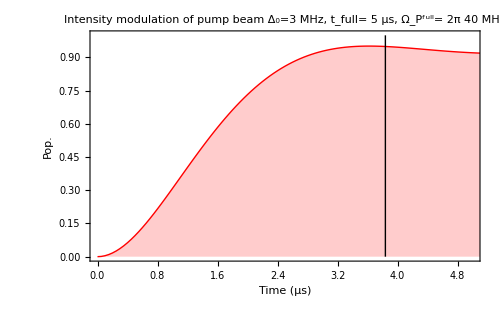

```mathematica
center=3MHz;
full=5μs;
ΩpMax=2π 40 MHz;
timeRes=(2π MHz)/ΩpMax FindRoot[scanΩpInterp[x]-center/MHz,{x,30}]⟦1,2⟧full/μs;
test1=findPops[2π 222 MHz,ΩpMax (1-t/full) ,center,0];
ListPlot[test1⟦4⟧,PlotRange->{{0,full/μs},{0,1}},Filling-> Axis,FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["Intensity modulation of pump beam \n Δ_0=`` MHz, t_full= `` μs, Ω_P^full= 2π `` MHz",center/MHz,full/μs,ΩpMax/(2π MHz)],Epilog->Line[{{timeRes,0},{timeRes,1}}]]
```

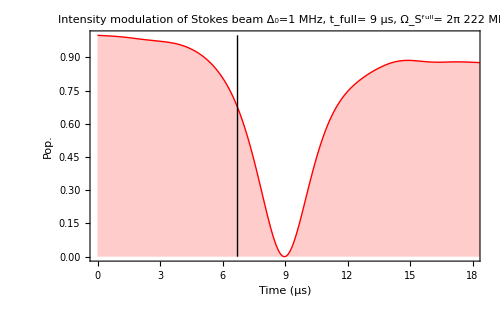

```mathematica
center=1MHz;
full=9μs;
ΩsMax=2π 222 MHz;
timeRes=(2π MHz)/ΩsMax FindRoot[scanΩsInterp[x]-center/MHz,{x,160}]⟦1,2⟧full/μs;
test1=findPops[Piecewise[{{ΩsMax t/full,t/full≤ 1},{ΩsMax(2-t/full),t/full>1}}], 2π 37 MHz,center,0];
ListPlot[test1⟦1⟧,PlotRange->{{0,2 full/μs},{0,1}},Filling-> Axis,FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["Intensity modulation of Stokes beam \n Δ_0=`` MHz, t_full= `` μs, Ω_S^full= 2π `` MHz",center/MHz,full/μs,ΩsMax/(2π MHz)],Epilog->Line[{{timeRes,0},{timeRes,1}}]]
```

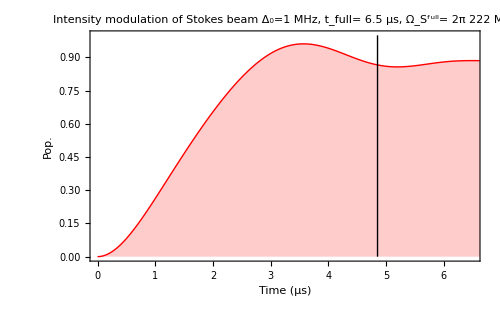

```mathematica
center=1MHz;
full=6.5μs;
ΩsMax=2π 222 MHz;
timeRes=(2π MHz)/ΩsMax FindRoot[scanΩsInterp[x]-center/MHz,{x,160}]⟦1,2⟧full/μs;
test1=findPops[ΩsMax (1-t/full), 2π 37 MHz,center,0];
ListPlot[test1⟦4⟧,PlotRange->{{0,full/μs},{0,1}},Filling-> Axis,FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["Intensity modulation of Stokes beam \n Δ_0=`` MHz, t_full= `` μs, Ω_S^full= 2π `` MHz",center/MHz,full/μs,ΩsMax/(2π MHz)],Epilog->Line[{{timeRes,0},{timeRes,1}}]]
```

```mathematica
center=3MHz;
full=5μs;
ΩpMax=2π 40 MHz;
timeRes=(2π MHz)/ΩpMax FindRoot[scanΩpInterp[x]-center/MHz,{x,30}]⟦1,2⟧full/μs;
test1=findPops[2π 222 MHz,Piecewise[{{ΩpMax t/full,t/full≤ 1},{ΩpMax(2-t/full),t/full>1}}] ,center,0];
test2=findPops[1.04 2π 222 MHz,Piecewise[{{ΩpMax t/full,t/full≤ 1},{ΩpMax(2-t/full),t/full>1}}] ,center,0];
test3=findPops[0.96 2π 222 MHz,Piecewise[{{ΩpMax t/full,t/full≤ 1},{ΩpMax(2-t/full),t/full>1}}] ,center,0];
```

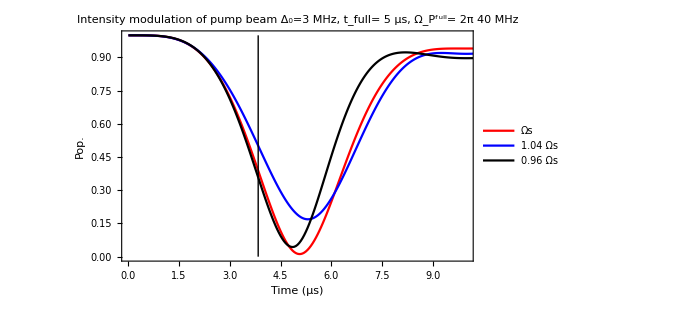
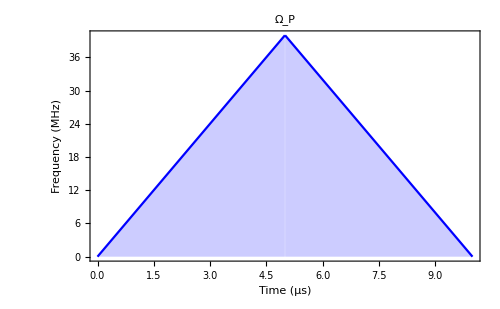

```mathematica
TableForm[{ListPlot[{test1⟦1⟧,test2⟦1⟧,test3⟦1⟧},PlotRange->{{0,2 full/μs},{0,1}},Filling-> None,FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["Intensity modulation of pump beam \n Δ_0=`` MHz, t_full= `` μs, Ω_P^full= 2π `` MHz",center/MHz,full/μs,ΩpMax/(2π MHz)],Epilog->Line[{{timeRes,0},{timeRes,1}}],PlotLegends->{"Ωs","1.04 Ωs","0.96 Ωs"}],
Plot[Piecewise[{{ΩpMax/(2π MHz) (t μs)/full,(t μs)/full≤ 1},{ΩpMax/(2π MHz)(2-(t μs)/full),(t μs)/full>1}}],{t,0,2 full/μs},PlotStyle->Blue,Filling->Axis,PlotLabel->"Ω_P",FrameLabel->{"Time (μs)","Frequency (MHz)"}]}]
```

```mathematica
center=3.MHz;
full=5μs;
ΩpMax=2π 40 MHz;
timeRes=(2π MHz)/ΩpMax FindRoot[scanΩpInterp[x]-center/MHz,{x,30}]⟦1,2⟧full/μs;
test1=findPops[2π 222 MHz,Piecewise[{{ΩpMax (1-t/full),t/full≤ 1},{ΩpMax(-1+t/full),t/full>1}}],center,0];
test2=findPops[1.04 2π 222 MHz,Piecewise[{{ΩpMax (1-t/full),t/full≤ 1},{ΩpMax(-1+t/full),t/full>1}}],center,0];
test3=findPops[0.96 2π 222 MHz,Piecewise[{{ΩpMax (1-t/full),t/full≤ 1},{ΩpMax(-1+t/full),t/full>1}}],center,0];
```

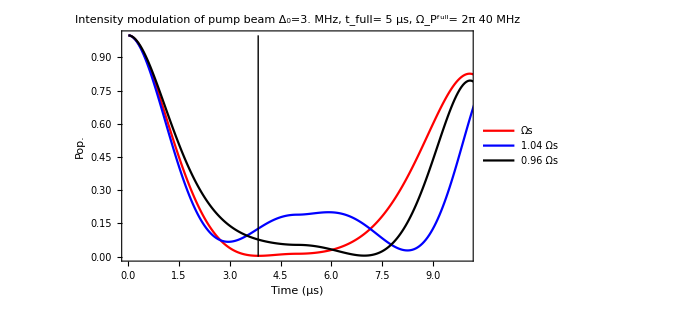
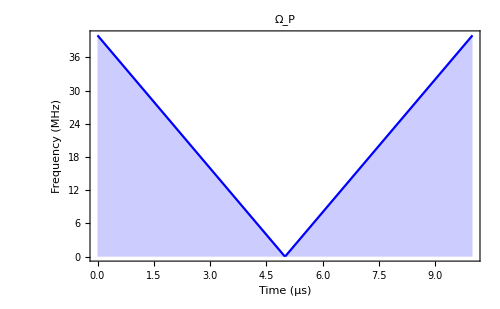

```mathematica
TableForm[{ListPlot[{test1⟦1⟧,test2⟦1⟧,test3⟦1⟧},PlotRange->{{0,2 full/μs},{0,1}},Filling-> None,FrameLabel->{"Time (μs)","Pop."},PlotLegends->{"Ωs","1.04 Ωs","0.96 Ωs"},PlotLabel->StringForm["Intensity modulation of pump beam \n Δ_0=`` MHz, t_full= `` μs, Ω_P^full= 2π `` MHz",center/MHz,full/μs,ΩpMax/(2π MHz)],Epilog->Line[{{timeRes,0},{timeRes,1}}]],
Plot[Piecewise[{{ΩpMax/(2π MHz)(1-(t  μs)/full),(t μs)/full≤ 1},{ΩpMax/(2π MHz)(-1+(t μs)/full),(t μs)/full>1}}],{t,0,2 full/μs},PlotStyle->Blue,Filling->Axis,PlotLabel->"Ω_P",FrameLabel->{"Time (μs)","Frequency (MHz)"}]}]
```

```mathematica
center=2.2MHz;
full=5μs;
ΩpMax=2π 40 MHz;
timeRes=(2π MHz)/ΩpMax FindRoot[scanΩpInterp[x]-center/MHz,{x,30}]⟦1,2⟧full/μs;
dev=0.2;
test1=findPops[Piecewise[{{Ωs Max( 1-dev t/full),t/full≤ 1},{Ωs Max( -dev+t/full),t/full>1}}],Piecewise[{{ΩpMax t/full,t/full≤ 1},{ΩpMax(2-t/full),t/full>1}}],center,0];
test2=findPops[ Piecewise[{{1.04Ωs Max( 1-dev t/full),t/full≤ 1},{1.04Ωs Max( -dev+t/full),t/full>1}}],,Piecewise[{{ΩpMax t/full,t/full≤ 1},{ΩpMax(2-t/full),t/full>1}}],center,0];
test3=findPops[Piecewise[{{0.96Ωs Max( 1-dev t/full),t/full≤ 1},{0.96Ωs Max( -dev+t/full),t/full>1}}],,Piecewise[{{ΩpMax t/full,t/full≤ 1},{ΩpMax(2-t/full),t/full>1}}] ,center,0];
```

InterpolatingFunction::dmval: Input value {46.2159} lies outside the range of data in the interpolating function. Extrapolation will be used.

$Aborted

NDSolveValue::nlnum: The function value {-1.02644+0. ⅈ,-829047.-10592.4 ⅈ,-3.33688×10^6-36693.3 ⅈ,(0.-1. ⅈ) ((0.+0. ⅈ)-(0.+3.14153×10^-6 ⅈ) Max Ωs)} is not a list of numbers with dimensions {4} at {t,p1[t],p2[t],p3[t],p4[t]} = {5.×10^-10,1.+0. ⅈ,0.-6.28319×10^-6 ⅈ,0.-0.0000217656 ⅈ,0.+0. ⅈ}.

$Aborted

```mathematica
TableForm[{ListPlot[{test1⟦4⟧,test2⟦4⟧,test3⟦4⟧},PlotRange->{{0,full/μs},{0,1}},Filling-> None,FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["sity modulation of pump beam \n Δ_0=`` MHz, t_full= `` μs, Ω_P^full= 2π `` MHz",center/MHz,full/μs,ΩpMax/(2π MHz)],Epilog->Line[{{timeRes,0},{timeRes,1}}],PlotLegends->{"Ωs","1.04 Ωs","0.96 Ωs"}],
Plot[Piecewise[{{ΩpMax/(2π MHz) (t μs)/full,(t μs)/full≤ 1},{ΩpMax/(2π MHz)(2-(t μs)/full),(t μs)/full>1}}],{t,0,full/μs},PlotStyle->Blue,Filling->Axis,PlotLabel->"Ω_P",FrameLabel->{"Time (μs)","Frequency (MHz)"}]}]
```

ListPlot::lpn: {{{0.,2.61012×10^-54},{0.05,2.74858×10^-8},{0.1,4.38034×10^-7},{0.15,2.20772×10^-6},{0.2,6.94287×10^-6},{0.25,0.0000168572},{0.3,0.0000347452},{0.35,0.0000639519},«35»,{2.15,0.0613316},{2.2,0.0664734},{2.25,0.0719075},{2.3,0.0776437},{2.35,0.0836917},{2.4,0.0900618},{2.45,0.096764},«351»},{},{}} is not a list of numbers or pairs of numbers.

$Aborted